t	Рунге-Кутт2	 x(t)	 отклонение

0	1	1	0

0.1	1.005	1.00501	0.0000125209

0.2	1.02015	1.0202	0.000050965

0.3	1.04591	1.04603	0.000118688

0.4	1.08307	1.08329	0.000221972

0.5	1.13278	1.13315	0.00037067

0.6	1.19664	1.19722	0.000579232

0.7	1.27675	1.27762	0.00086826

0.8	1.37586	1.37713	0.00126675

0.9	1.49749	1.4993	0.00181538

1.	1.64615	1.64872	0.00257111

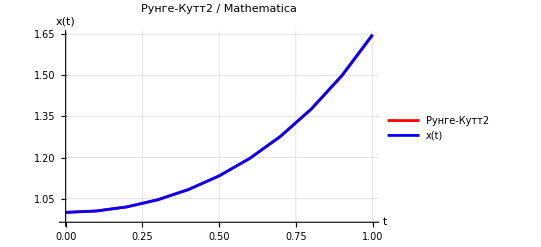

```mathematica
f[t_,x_]:=t*x;

fe[t_]:=Exp[t^2/2]; (*f_e*)
a=0;
b=1;
t0=0;
x0=1;
h=0.1;

pointst={t0};  
pointsx={x0};  
points={x0}; 

While[t0<b,x0+=h*f[t0+h/2,x0+h/2*f[t0,x0]];
AppendTo[pointst,t0+h];
AppendTo[pointsx,x0];
AppendTo[points,fe[t0+h]];
t0+=h;];

Print["t\tРунге-Кутт2\t x(t)\t отклонение"];
Do[Print[pointst[[i]],"\t",pointsx[[i]],"\t",points[[i]],"\t",Abs[pointsx[[i]]-points[[i]]]],{i,Length[pointst]}];

ListLinePlot[{Transpose[{pointst,pointsx}],Transpose[{pointst,points}]},PlotLegends->{"Рунге-Кутт2"," x(t)"},AxesLabel->{"t","x(t)"},PlotLabel->"Рунге-Кутт2 / Mathematica",GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],PlotStyle->{Red,Blue}]
```

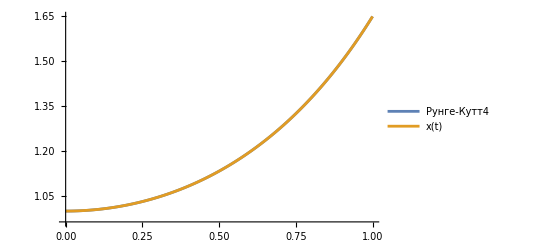

t | Рунге-Кутт4 | x(t) | разница
0 | 1 | 1 | 0
0.01 | 1.00005 | 1.00005 | 0.
0.02 | 1.0002 | 1.0002 | 0.
0.03 | 1.00045 | 1.00045 | 0.
0.04 | 1.0008 | 1.0008 | 0.
0.05 | 1.00125 | 1.00125 | 2.22045×10^-16
0.06 | 1.0018 | 1.0018 | 2.22045×10^-16
0.07 | 1.00245 | 1.00245 | 2.22045×10^-16
0.08 | 1.00321 | 1.00321 | 4.44089×10^-16
0.09 | 1.00406 | 1.00406 | 4.44089×10^-16
0.1 | 1.00501 | 1.00501 | 4.44089×10^-16
0.11 | 1.00607 | 1.00607 | 6.66134×10^-16
0.12 | 1.00723 | 1.00723 | 8.88178×10^-16
0.13 | 1.00849 | 1.00849 | 1.11022×10^-15
0.14 | 1.00985 | 1.00985 | 1.33227×10^-15
0.15 | 1.01131 | 1.01131 | 1.33227×10^-15
0.16 | 1.01288 | 1.01288 | 1.77636×10^-15
0.17 | 1.01455 | 1.01455 | 1.9984×10^-15
0.18 | 1.01633 | 1.01633 | 2.66454×10^-15
0.19 | 1.01821 | 1.01821 | 3.10862×10^-15
0.2 | 1.0202 | 1.0202 | 3.77476×10^-15
0.21 | 1.02229 | 1.02229 | 4.44089×10^-15
0.22 | 1.0245 | 1.0245 | 5.32907×10^-15
0.23 | 1.0268 | 1.0268 | 6.43929×10^-15
0.24 | 1.02922 | 1.02922 | 7.77156×10^-15
0.25 | 1.03174 | 1.03174 | 9.10383×10^-15
0.26 | 1.03438 | 1.03438 | 1.06581×10^-14
0.27 | 1.03712 | 1.03712 | 1.24345×10^-14
0.28 | 1.03998 | 1.03998 | 1.46549×10^-14
0.29 | 1.04295 | 1.04295 | 1.70974×10^-14
0.3 | 1.04603 | 1.04603 | 1.9984×10^-14
0.31 | 1.04922 | 1.04922 | 2.33147×10^-14
0.32 | 1.05253 | 1.05253 | 2.70894×10^-14
0.33 | 1.05596 | 1.05596 | 3.15303×10^-14
0.34 | 1.0595 | 1.0595 | 3.66374×10^-14
0.35 | 1.06316 | 1.06316 | 4.24105×10^-14
0.36 | 1.06695 | 1.06695 | 4.90719×10^-14
0.37 | 1.07085 | 1.07085 | 5.63993×10^-14
0.38 | 1.07487 | 1.07487 | 6.50591×10^-14
0.39 | 1.07902 | 1.07902 | 7.43849×10^-14
0.4 | 1.08329 | 1.08329 | 8.50431×10^-14
0.41 | 1.08768 | 1.08768 | 9.70335×10^-14
0.42 | 1.09221 | 1.09221 | 1.10578×10^-13
0.43 | 1.09686 | 1.09686 | 1.25677×10^-13
0.44 | 1.10164 | 1.10164 | 1.42775×10^-13
0.45 | 1.10655 | 1.10655 | 1.61648×10^-13
0.46 | 1.1116 | 1.1116 | 1.82965×10^-13
0.47 | 1.11678 | 1.11678 | 2.06501×10^-13
0.48 | 1.1221 | 1.1221 | 2.32703×10^-13
0.49 | 1.12755 | 1.12755 | 2.61569×10^-13
0.5 | 1.13315 | 1.13315 | 2.93765×10^-13
0.51 | 1.13889 | 1.13889 | 3.29292×10^-13
0.52 | 1.14477 | 1.14477 | 3.68372×10^-13
0.53 | 1.15079 | 1.15079 | 4.11671×10^-13
0.54 | 1.15696 | 1.15696 | 4.5941×10^-13
0.55 | 1.16329 | 1.16329 | 5.11813×10^-13
0.56 | 1.16976 | 1.16976 | 5.69544×10^-13
0.57 | 1.17639 | 1.17639 | 6.32827×10^-13
0.58 | 1.18317 | 1.18317 | 7.02327×10^-13
0.59 | 1.19012 | 1.19012 | 7.78266×10^-13
0.6 | 1.19722 | 1.19722 | 8.61311×10^-13
0.61 | 1.20448 | 1.20448 | 9.52127×10^-13
0.62 | 1.21191 | 1.21191 | 1.05116×10^-12
0.63 | 1.21951 | 1.21951 | 1.15907×10^-12
0.64 | 1.22728 | 1.22728 | 1.27676×10^-12
0.65 | 1.23522 | 1.23522 | 1.40465×10^-12
0.66 | 1.24334 | 1.24334 | 1.54343×10^-12
0.67 | 1.25163 | 1.25163 | 1.69442×10^-12
0.68 | 1.26011 | 1.26011 | 1.85829×10^-12
0.69 | 1.26877 | 1.26877 | 2.0357×10^-12
0.7 | 1.27762 | 1.27762 | 2.228×10^-12
0.71 | 1.28666 | 1.28666 | 2.43605×10^-12
0.72 | 1.29589 | 1.29589 | 2.66098×10^-12
0.73 | 1.30532 | 1.30532 | 2.9039×10^-12
0.74 | 1.31495 | 1.31495 | 3.16636×10^-12
0.75 | 1.32478 | 1.32478 | 3.44924×10^-12
0.76 | 1.33482 | 1.33482 | 3.75455×10^-12
0.77 | 1.34508 | 1.34508 | 4.0834×10^-12
0.78 | 1.35554 | 1.35554 | 4.43734×10^-12
0.79 | 1.36622 | 1.36622 | 4.81815×10^-12
0.8 | 1.37713 | 1.37713 | 5.2276×10^-12
0.81 | 1.38826 | 1.38826 | 5.66769×10^-12
0.82 | 1.39962 | 1.39962 | 6.13998×10^-12
0.83 | 1.41121 | 1.41121 | 6.64735×10^-12
0.84 | 1.42305 | 1.42305 | 7.19136×10^-12
0.85 | 1.43512 | 1.43512 | 7.77467×10^-12
0.86 | 1.44745 | 1.44745 | 8.3995×10^-12
0.87 | 1.46002 | 1.46002 | 9.06875×10^-12
0.88 | 1.47285 | 1.47285 | 9.78528×10^-12
0.89 | 1.48594 | 1.48594 | 1.05516×10^-11
0.9 | 1.4993 | 1.4993 | 1.13711×10^-11
0.91 | 1.51293 | 1.51293 | 1.22469×10^-11
0.92 | 1.52684 | 1.52684 | 1.31826×10^-11
0.93 | 1.54103 | 1.54103 | 1.41815×10^-11
0.94 | 1.5555 | 1.5555 | 1.5248×10^-11
0.95 | 1.57027 | 1.57027 | 1.63858×10^-11
0.96 | 1.58534 | 1.58534 | 1.75988×10^-11
0.97 | 1.60071 | 1.60071 | 1.88924×10^-11
0.98 | 1.6164 | 1.6164 | 2.02705×10^-11
0.99 | 1.6324 | 1.6324 | 2.17386×10^-11
1. | 1.64872 | 1.64872 | 2.33018×10^-11

```mathematica
f[t_,x_]:=t*x;

fe[t_]:=Exp[t^2/2]; (*f_e*)

t0=0;
x0=1;
a=0;
b=1;
h=0.01; 

pointsT={t0};
pointsX={x0};
points={x0};

While[t0<b,k1=h*f[t0,x0];
k2=h*f[t0+h/2,x0+k1/2];
k3=h*f[t0+h/2,x0+k2/2];
k4=h*f[t0+h,x0+k3];
x0=x0+1/6*(k1+2*k2+2*k3+k4);
AppendTo[pointsT,t0+h];
AppendTo[pointsX,x0];
AppendTo[points,fe[t0+h]];
t0=t0+h;]

ListLinePlot[{Transpose[{pointsT,pointsX}],Transpose[{pointsT,points}]},PlotLegends->{"Рунге-Кутт4","x(t)"}]

TableForm[Table[{pointsT[[i]],pointsX[[i]],points[[i]],Abs[pointsX[[i]]-points[[i]]]},{i,Length[pointsT]}],TableHeadings->{None,{"t","Рунге-Кутт4","x(t)","разница"}}]
```

```mathematica
(*рунге кутт4 го для уравнения . систему лоренца (инт кривые и фаз траекторию \ )*)
```